```mathematica
tahiti=Import["/users/pp/Desktop/tahiti.txt", "table"];
darwin=Import["/users/pp/Desktop/darwin0.txt", "table"];
NINO34=Import["/users/pp/github/context/Mathematica/SOIM/data/nino34ke.txt", "table"];
```

{char t,4.07278,0.24652, Years from,1880.5,to,1988.33,CC,82.624,61.9955,-20.6285}

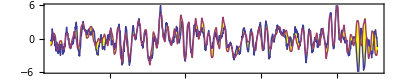

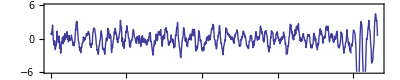

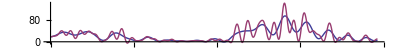

6.38535

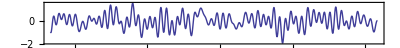

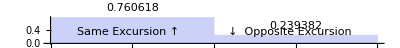

-Graphics-

```mathematica
dilate[x_] := - 0.11*Sin[2*Pi*x+1.1];
Window = 7;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
STRT=6; STRTY=1880+STRT/12;LNGTH=1300; ENDY=1880+LNGTH/12; 
QBW=2.331;     TR = 199.0;  CF = 2.38;  OSC := 9.30;  CW =0.9698;  NL =0.05;
diu[x_] := 0.33*Cos[2*Pi/OSC*x+5.5]+0.06*Cos[Pi/(2*OSC)*x+4.7]-0.2*Cos[2*Pi*x/(3*OSC)-0.2];
qbw[x_] := +0.045*Cos[2*Pi/7*x+1.9]+0.17*Cos[2*Pi/QBW*x+2.8] +0.08*Sin[2*Pi/2.246*x+0.1] -0.05*Cos[2*Pi/2.117*x-0.9] -0.03*Cos[2*Pi/3.58*x-1.6]-0.1*Cos[2*Pi/2.903*x-0.7]   ;
cw[x_] := Sin[CW*(x+2.)+ 0.111*Sin[0.38*(x+6.4)] +0.4] *(1+0.34*Sin[0.097*x-0.8]) ; 
cwb[x_] := -0.57*cw[x+0.22]+0.23*cw[x/2+1.5] + 0.11*Cos[2*Pi/5.79*x+1.4] ;  
RHS[x_] := 3.1*qbw[x-0.04]+1*0.4*cwb[x-0.24]-0.86*diu[x-1.2]+0.13*Cos[2*Pi/52*x+4.3] -0.15*Sin[2*Pi/21.0*x+4.2]+  0.2*Cos[2*Pi/7.333*x+3.0] ;  
lhs=Table[{1880.0+x,  (12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-CF*R[[x*12]]+NL*(R[[x*12]])^2)},{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, -3*RHS[x+dilate[x]+0.78]+0.02*DiracDelta[x-100]},  {x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, -If[x>99.1&&x<112,1,1]*3*RHS[x+dilate[x]+0.78]},  {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-6,6},Frame->True,Axes->True, Filling->{1->{{2},Yellow}}, PlotLegends->{"LHS","RHS"},AspectRatio->0.2] 
SDIF = lhs[[All,2]]-rhs[[All,2]];  
ListLinePlot[{SDIF},PlotRange->{-6,6},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.2] 
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,400,800,400}],{ω,0.0,π/5/2},PlotRange->All,AspectRatio->0.1] 
2*Pi/0.082/12
ListLinePlot[{Table[{1880.0+x, RHS[x]},{x,1/12,135.0, 1/12}]}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"RHS"}]
SBIN = Abs[Sign[lhs[[All,2]]]- Sign[rhs[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.1,   ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,400,800,400}],{ω,0.0,π/5/2},PlotRange->All,AspectRatio->0.1]
```

{4.60705 = char t,0.0153858 =err,1880.5  .. ,1988.33,CC,61.9955,58.947,-3.04848}

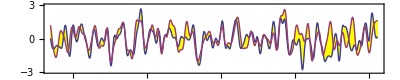

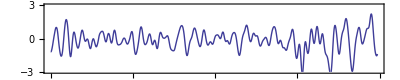

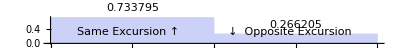

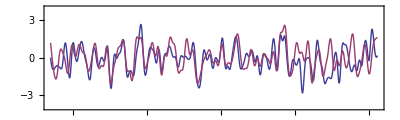

```mathematica
STRT=12; LNGTH=1600; 
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
 IC=52.5;  SHFT=0.91;
CF = 1.86; NL=0.0029;
(* RHS[x_] := 1*4.2*qbw[x+0.0]+1*0.55*cwb[x-0.23]-1*3.2*Osc[x-1.0] + 0.07*tsi[x-0.3]-0.2*Cos[2*Pi/22*x+3.3] + 0.3*Cos[2*Pi/7.333*x+3.0];  *)
SOLN=NDSolve[{y''[x]+CF*y[x]-NL*(y[x])^2 == -92.3*RHS[x-0.0] -10.4*DiracDelta[x-101.9], 
                               y'[IC]==-52.0, y[IC]==+23.1}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, +0.028*(First[y[x+SHFT] /. SOLN])},{x, STRT/12-0,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-3,3},Frame->True,Axes->True, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
ListLinePlot[{SDIF},PlotRange->{-3,3},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.2] 
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.1,
   ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4},Frame->True,Axes->False,       PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.3]
```

{char t,4.14301,0.0165176, Years from,1880.5,to,1980.,CC,58.947,79.61,20.663}

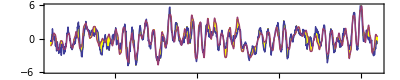

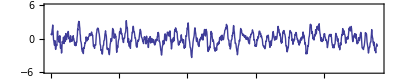

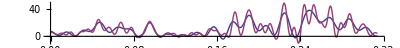

6.38535

-Graphics-

2.38039

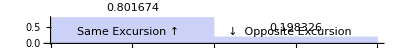

-Graphics-

```mathematica
dilate[x_] := - 0.11*Sin[2*Pi*x+1.1];
Window = 7;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
STRT=6; STRTY=1880+STRT/12;LNGTH=1200; ENDY=1880+LNGTH/12; 
QBW=2.331;     TR = 199.0;  CF = 2.3;  OSC := 9.30;  CW =0.9698; 
diu[x_] := 0.33*Cos[2*Pi/OSC*x+5.5]+0.06*Cos[Pi/(2*OSC)*x+4.7]-0.2*Cos[2*Pi*x/(3*OSC)-0.2];
qbw[x_] := +0.045*Cos[2*Pi/7*x+1.9]+0.17*Cos[2*Pi/QBW*x+2.8] +0.08*Sin[2*Pi/2.246*x+0.1] -0.05*Cos[2*Pi/2.117*x-0.9] -0.03*Cos[2*Pi/3.58*x-1.6]-0.1*Cos[2*Pi/2.903*x-0.7]   ;
cw[x_] := Sin[CW*(x+2.)+ 0.119*Sin[0.36*(x+6.8)] +0.5] *(1+0.31*Sin[0.093*x-0.2]) ; 
cw[x_] := Sin[CW*(x+2.)+ 0.111*Sin[0.38*(x+6.4)] +0.4] *(1+0.34*Sin[0.097*x-0.8]) ; 
cwb[x_] := -0.57*cw[x+0.22]+0.23*cw[x/2+1.5] + 0.11*Cos[2*Pi/5.79*x+1.4] ;  
RHS[x_] := 3.1*qbw[x-0.04]+1*0.4*cwb[x-0.24]-0.86*diu[x-1.2]+0.13*Cos[2*Pi/52*x+4.3] -0.15*Sin[2*Pi/21.0*x+4.2]+  0.2*Cos[2*Pi/7.333*x+3.0] ;  
lhs=Table[{1880.0+x,  (12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-CF*R[[x*12]])},{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, -If[x>99.1&&x<112,-2.2*Exp[-(x-99.1)/7.1],1]*3*RHS[x+dilate[x]+0.78]},  {x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, -If[x>99.1&&x<112,1,1]*3*RHS[x+dilate[x]+0.78]},  {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-6,6},Frame->True,Axes->True, Filling->{1->{{2},Yellow}}, PlotLegends->{"LHS","RHS"},AspectRatio->0.2] 
SDIF = lhs[[All,2]]-rhs[[All,2]];  
ListLinePlot[{SDIF},PlotRange->{-6,6},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.2] 
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,400,800,400}],{ω,0.0,π/5/2},PlotRange->All,AspectRatio->0.1] 
2*Pi/0.082/12
ListLinePlot[{Table[{1880.0+x, RHS[x]},{x,1/12,135.0, 1/12}]}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"RHS"}]
100.0/42.01
SBIN = Abs[Sign[lhs[[All,2]]]- Sign[rhs[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.1,
   ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,400,800,400}],{ω,0.0,π/5/2},PlotRange->All,AspectRatio->0.1]
```

{char t,4.14301,0.185671, Years from,1978.33,to,2013.33,CC,79.61,74.754,-4.85593}

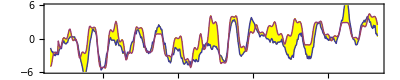

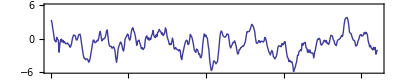

6.38535

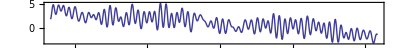

2.38039

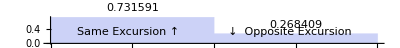

```mathematica
dilate[x_] := - 0.11*Sin[2*Pi*x+0.7];
Window = 7;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
STRT=1180; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
QBW=2.331;     TR = 199.0;  CF = 2.3;  OSC := 9.30;  CW =0.9698; 
diu[x_] := 0.33*Cos[2*Pi/OSC*x+5.5]+0.06*Cos[Pi/(2*OSC)*x+4.7]-0.2*Cos[2*Pi*x/(3*OSC)-0.2];
qbw[x_] := +0.045*Cos[2*Pi/7*x+1.9]+0.17*Cos[2*Pi/QBW*x+2.8] +0.08*Sin[2*Pi/2.246*x+0.1] -0.05*Cos[2*Pi/2.117*x-0.9] -0.03*Cos[2*Pi/3.58*x-1.6]-0.1*Cos[2*Pi/2.903*x-0.7]   ;
cw[x_] := Sin[CW*(x+2.)+ 0.111*Sin[0.38*(x+6.4)] +0.4] *(1+0.34*Sin[0.097*x-0.8]) ; 
cwb[x_] := -0.57*cw[x+0.22]+0.23*cw[x/2+1.5] + 0.11*Cos[2*Pi/5.79*x+1.4] ;  
(*RHS[x_]:=3.1*qbw[x-0.04]+1*0.4*cwb[x-0.24]-0.86*diu[x-1.2]+0.13*Cos[2*Pi/52*x+4.3] -0.15*Sin[2*Pi/21.0*x+4.2]+0.2*Cos[2*Pi/7.333*x+3.0] ;  *)
RHS[x_] := 6.9*qbw[x+0.14]+1*0.5*cwb[x-0.24]-0.9*diu[x-1.2]+0.5*Cos[2*Pi/52*x+0.3] -0.15*Sin[2*Pi/21.0*x+4.2]+0.2*Cos[2*Pi/7.333*x+3.0]-(x-100)*.034;  
lhs=Table[{1880.0+x,  (12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-CF*R[[x*12]])},{x,STRT/12,LNGTH/12, 1/12}];     
rhs=Table[{1880.0+x, -1.3-1.8*If[x>99.1&&x<115,-1,1]*RHS[x+1.9*dilate[x]+0.8]},  {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-6,6},Frame->True,Axes->True, Filling->{1->{{2},Yellow}}, PlotLegends->{"LHS","RHS"},AspectRatio->0.2] 
SDIF = lhs[[All,2]]-rhs[[All,2]];  
ListLinePlot[{SDIF},PlotRange->{-6,6},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.2] 
2*Pi/0.082/12
ListLinePlot[{Table[{1880.0+x, RHS[x]},{x,1/12,135.0, 1/12}]}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"RHS"}]
100.0/42.01
SBIN = Abs[Sign[lhs[[All,2]]]- Sign[rhs[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.1,   ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```

{char t,4.14301,-0.850182, Years from,1978.33,to,2013.33,CC,74.754,82.6633,7.90931}

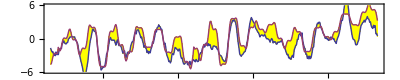

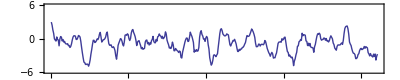

6.38535

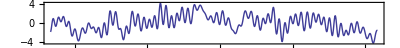

133.685

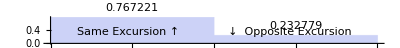

```mathematica
dilate[x_] := - 0.11*Sin[2*Pi*x+0.7];
Window = 7;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
STRT=1180; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
QBW=2.331;     TR = 199.0;  CF = 2.3;  OSC := 9.30;  CW =0.9698; 
diu[x_] := 0.33*Cos[2*Pi/OSC*x+5.5]+0.06*Cos[Pi/(2*OSC)*x+4.7]-0.2*Cos[2*Pi*x/(3*OSC)-0.2];
qbw[x_] := +0.045*Cos[2*Pi/7*x+1.9]+0.17*Cos[2*Pi/QBW*x+2.8] +0.08*Sin[2*Pi/2.246*x+0.1] -0.05*Cos[2*Pi/2.117*x-0.9] -0.03*Cos[2*Pi/3.58*x-1.6]-0.1*Cos[2*Pi/2.903*x-0.7]   ;
cw[x_] := Sin[CW*(x+2.)+ 0.111*Sin[0.38*(x+6.4)] +0.4] *(1+0.34*Sin[0.097*x-0.8]) ; 
cwb[x_] := -0.57*cw[x+0.22]+0.23*cw[x/2+1.5] + 0.11*Cos[2*Pi/5.79*x+1.4] ;  
(*RHS[x_]:=3.1*qbw[x-0.04]+1*0.4*cwb[x-0.24]-0.86*diu[x-1.2]+0.13*Cos[2*Pi/52*x+4.3] -0.15*Sin[2*Pi/21.0*x+4.2]+0.2*Cos[2*Pi/7.333*x+3.0] ;  *)
RHS[x_] := 6.1*qbw[x+0.16]+1*0.5*cwb[x+0.44]-2.5*diu[x-1.2]+0.7*Cos[2*Pi/54*x-0.0] -0.6*Sin[2*Pi/21.0*x+4.4]+0.2*Cos[2*Pi/7.333*x+3.0] +
                                                                                       0.65*Sin[2*Pi/11.01*x-0.61]  - 1.2*Sin[(x-99)*.047];  
lhs=Table[{1880.0+x,  (12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-CF*R[[x*12]])},{x,STRT/12,LNGTH/12, 1/12}];     
rhs=Table[{1880.0+x, -1.93*(1+1*If[x>99.1&&x<113.6,-1,1]*RHS[x+1.7*dilate[x]+0.82])},  {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-6,6},Frame->True,Axes->True, Filling->{1->{{2},Yellow}}, PlotLegends->{"LHS","RHS"},AspectRatio->0.2] 
SDIF = lhs[[All,2]]-rhs[[All,2]];  
ListLinePlot[{SDIF},PlotRange->{-6,6},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.2] 
2*Pi/0.082/12
ListLinePlot[{Table[{1880.0+x, RHS[x]},{x,1/12,135.0, 1/12}]}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"RHS"}]
2*Pi/0.047
SBIN = Abs[Sign[lhs[[All,2]]]- Sign[rhs[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.1,   ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```

Correlation::vctmat: The arguments to Correlation are not a pair of vectors or a pair of matrices of equal length.

{4.5345 = char t,-0.70275 =err,1978.33  .. ,2013.33,CC,82.6633,{198008.,-202.868},{197926.,-285.532}}

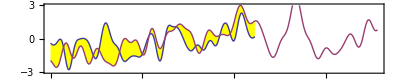

Thread::tdlen: Objects of unequal length in {-0.412727, -0.452727, -0.490736, -0.525714, -0.5529, -0.570909, -0.577749, -0.573247, -0.557143, -0.529784, -0.491861, -0.444156, « 27 », -2.52684, -2.3374, -2.11749, -1.87991, -1.63351, -1.38554, -1.14788, -0.931255, -0.737749, -0.568658, -0.42658, « 351 »} + {« 1 »} cannot be combined.

-Graphics-

```mathematica
STRT=1200; LNGTH=1600; 
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
 IC=52.5;  SHFT=1.05;
CF = 1.92;
(* RHS[x_] := 1*4.2*qbw[x+0.0]+1*0.55*cwb[x-0.23]-1*3.2*Osc[x-1.0] + 0.07*tsi[x-0.3]-0.2*Cos[2*Pi/22*x+3.3] + 0.3*Cos[2*Pi/7.333*x+3.0];  *)
SOLN=NDSolve[{y''[x]+CF*y[x]== -133.3*RHS[x+0.0] + 50.3*DiracDelta[x-100.2] +(x-100)*1.1, 
                               y'[IC]==-40.1, y[IC]==-100.0}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, -1+0.012*If[x>100,1,1]*(First[y[x+SHFT] /. SOLN])},{x, STRT/12-0,LNGTH/12+20, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-3,3},Frame->True,Axes->True, Filling->{1->{{2},Yellow}},    PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
ListLinePlot[{SDIF},PlotRange->{-3,3},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.2]
```

{char t,4.81898,-0.0238019, Years from,1980.,to,2013.33,CC,{198008.,-202.868},73.6097,{-197935.,276.478}}

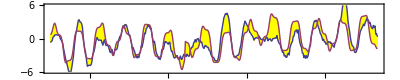

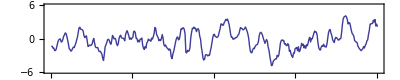

6.38535

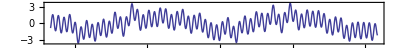

133.685

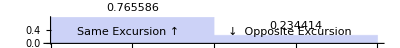

```mathematica
dilate[x_] := - 0.11*Sin[2*Pi*x+0.6];
Window = 7;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
STRT=1200; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
QBW=2.331;     TR = 199.0;  CF = 1.7;  OSC := 9.30;  CW =0.9698; 
diu[x_] := 0.33*Cos[2*Pi/OSC*x+5.5]+0.06*Cos[Pi/(2*OSC)*x+4.7]-0.2*Cos[2*Pi*x/(3*OSC)-0.2];
qbw[x_] := +0.045*Cos[2*Pi/7*x+1.9]+0.17*Cos[2*Pi/QBW*x+2.8] +0.08*Sin[2*Pi/2.246*x+0.1] -0.05*Cos[2*Pi/2.117*x-0.9] -0.03*Cos[2*Pi/3.58*x-1.6]-0.1*Cos[2*Pi/2.903*x-0.7]   ;
cw[x_] := Sin[CW*(x+2.)+ 0.111*Sin[0.38*(x+6.4)] +0.4] *(1+0.34*Sin[0.097*x-0.8]) ; 
cwb[x_] := -0.57*cw[x+0.22]+0.23*cw[x/2+1.5] + 0.11*Cos[2*Pi/5.79*x+1.4] ;  
(*RHS[x_]:=3.1*qbw[x-0.04]+1*0.4*cwb[x-0.24]-0.86*diu[x-1.2]+0.13*Cos[2*Pi/52*x+4.3] -0.15*Sin[2*Pi/21.0*x+4.2]+0.2*Cos[2*Pi/7.333*x+3.0] ;  *)
RHS[x_] := 6.4*qbw[x+0.15]+1*0.9*cwb[x+0.46]-1.1*diu[x-1.2]-0.5*Cos[2*Pi/55*x+4.3] -0.0*Sin[2*Pi/21.0*x+4.4]+0.18*Cos[2*Pi/7.333*x+3.0] +
                                                                                      0.0*Sin[2*Pi/11.01*x-0.9]  - 0.0*Sin[(x-99)*.047];  
RHS[x_] := 1.45*Sin[2*Pi/2.3334*x-1.09]+1*0.9*cwb[x+0.46]-1.4*diu[x-1.2]-1.2*Cos[2*Pi/55*x+4.42] -0.0*Sin[2*Pi/21.0*x+4.4]+0.18*Cos[2*Pi/7.333*x+3.0] +
                                                                                      0.0*Sin[2*Pi/11.01*x-0.9]  - 0.0*Sin[(x-99)*.047];  
lhs=Table[{1880.0+x,  (12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-CF*R[[x*12]] -0*0.2*(R[[x*12]])^2)},{x,STRT/12,LNGTH/12, 1/12}];     
rhs=Table[{1880.0+x, -2-2.0*(1*If[x>99.9&&x<113.7,-1,1]*RHS[x+1.4*dilate[x]+0.82])},  {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-6,6},Frame->True,Axes->True, Filling->{1->{{2},Yellow}}, PlotLegends->{"LHS","RHS"},AspectRatio->0.2] 
SDIF = lhs[[All,2]]-rhs[[All,2]];  
ListLinePlot[{SDIF},PlotRange->{-6,6},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.2] 
2*Pi/0.082/12
ListLinePlot[{Table[{1880.0+x, RHS[x]},{x,1/12,135.0, 1/12}]}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"RHS"}]
2*Pi/0.047
SBIN = Abs[Sign[lhs[[All,2]]]- Sign[rhs[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.1,   ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```

{char t,5.14739,0.0561416, Years from,1881.,to,2013.33,CC,73.6097,71.3614,-2.24827}

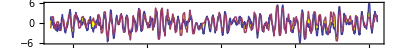

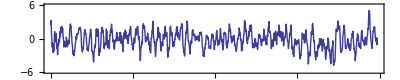

```mathematica
dilate[x_] := Sin[2*Pi*x+0.74];
Window = 7;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
STRT=12; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
QBW=2.331;     TR = 199.0;  CF = 1.49;  OSC := 9.30;  CW =0.9698; 
diu[x_] := 0.33*Cos[2*Pi/OSC*x+5.5]+0.06*Cos[Pi/(2*OSC)*x+4.7]-0.2*Cos[2*Pi*x/(3*OSC)-0.2];
qbw[x_] := +0.045*Cos[2*Pi/7*x+1.9]+0.17*Cos[2*Pi/QBW*x+2.8] +0.08*Sin[2*Pi/2.246*x+0.1] -0.05*Cos[2*Pi/2.117*x-0.9] -0.03*Cos[2*Pi/3.58*x-1.6]-0.1*Cos[2*Pi/2.903*x-0.7]   ;
cw[x_] := Sin[CW*(x+2.)+ 0.111*Sin[0.38*(x+6.4)] +0.4] *(1+0.34*Sin[0.097*x-0.8]) ; 
cwb[x_] := -0.57*cw[x+0.22]+0.23*cw[x/2+1.5] + 0.11*Cos[2*Pi/5.79*x+1.4] ;  
RHS[x_] := 3.1*qbw[x-0.04]+1*0.4*cwb[x-0.24]-0.86*diu[x-1.2]+0.13*Cos[2*Pi/52*x+4.3] -0.15*Sin[2*Pi/21.0*x+4.2]+  0.2*Cos[2*Pi/7.333*x+3.0] ;  
RHS[x_] := 7.8*qbw[x*1.0022-0.2] +1*0.4*cwb[x-0.1]-1.2*diu[x-0.7]-0.0*Cos[2*Pi/52*x-0.9] -0.0*Sin[2*Pi/21.0*x+4.2]+  0.0*Cos[2*Pi/7.0*x-1.0] ;  
lhs=Table[{1880.0+x,  (12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-CF*R[[x*12]]-0.0*(R[[x*12]])^3)},{x,STRT/12,LNGTH/12, 1/12}];     
rhs=Table[{1880.0+x, -If[x>99.9&&x<115.2,-1.01,1]*1.55*RHS[x-0.15*dilate[x]+0.79]},  {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-6,6},Frame->True,Axes->True, Filling->{1->{{2},Yellow}}, PlotLegends->{"LHS","RHS"},AspectRatio->0.1] 
SDIF = lhs[[All,2]]-rhs[[All,2]];  
ListLinePlot[{SDIF},PlotRange->{-6,6},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.2]
```

{char t,5.31026,0.385683, Years from,1881.,to,2013.33,CC,77.4867,74.0927,-3.39399}

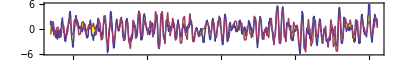

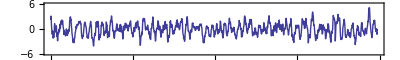

433.99

2.90888

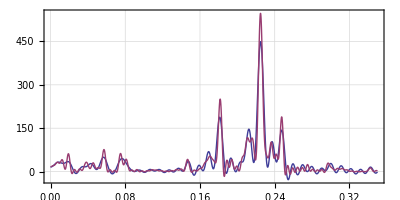

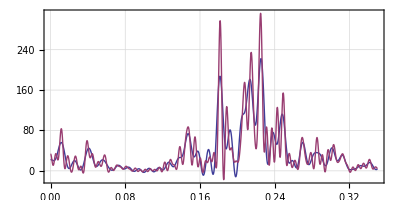

```mathematica
dilate[x_] := Sin[2*Pi*x+0.74];
Window = 7;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
(* Window = 6;  
R = MeanFilter[MeanFilter[MeanFilter[1.3*NINO34[[All,2]],Window],Window-2],Window-4]; *)
STRT=12; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
QBW=2.331;     TR = 99.0;  CF = 1.4;  OSC := 9.30;  CW =0.9698; 
diu[x_] := 0.33*Cos[2*Pi/OSC*x+5.5]+0.06*Cos[Pi/(2*OSC)*x+4.7]-0.2*Cos[2*Pi*x/(3*OSC)-0.2];
qbw[x_] := +0.045*Cos[2*Pi/7*x+1.9]+0.17*Cos[2*Pi/QBW*x+2.8] +0.08*Sin[2*Pi/2.246*x+0.1] -
           0.05*Cos[2*Pi/2.117*x-0.9] -0.03*Cos[2*Pi/3.58*x-1.6]-0.1*Cos[2*Pi/2.903*x-0.7]   ;
cw[x_] := Sin[CW*(x+2.)+ 0.111*Sin[0.38*(x+6.4)] +0.4] *(1+0.34*Sin[0.097*x-0.8]) ; 
cwb[x_] := -0.57*cw[x+0.22]+0.23*cw[x/2+1.5] + 0.11*Cos[2*Pi/5.79*x+1.4] ;  
(* CWP =6.45; cwbb[x_] := If[x>46.5, 0.9*Sin[2*Pi/CWP*(x+2.1) +0.1], 0.9*Sin[2*Pi/6.38*(x+2.1) +2.0]]; *)
(* RHS[x_] := 3.1*qbw[x-0.04]+1*0.4*cwb[x-0.24]-0.86*diu[x-1.2]+0.13*Cos[2*Pi/52*x+4.3] -0.15*Sin[2*Pi/21.0*x+4.2]+  0.2*Cos[2*Pi/7.333*x+3.0] ; *)
CWY = 1.1882;   (* 0.1 *)
RHS[x_] := (7.5*qbw[x*1.0019-0.22] +0.4*cwb[x+0.1]-1.2*diu[x-0.7] ) * (1+x*0.001) ;  
lhs=Table[{1880.0+x,  (12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-CF*If[x>LOW&&x<HI,1,1]*R[[x*12]])},
         {x,STRT/12,LNGTH/12, 1/12}]; 
LOW = 100.2; HI = 116.2;    
rhs=Table[{1880.0+x, If[x>LOW&&x<HI,-1.1,0]-If[x>LOW&&x<HI,-1,1]*1.42*RHS[x-0.16*dilate[x]+0.83]}, 
                  {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-6,6},Frame->True,Axes->True, Filling->{1->{{2},Yellow}}, PlotLegends->{"LHS","RHS"},AspectRatio->0.15] 
SDIF = lhs[[All,2]]-rhs[[All,2]];  
ListLinePlot[{SDIF},PlotRange->{-6,6},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.15] 
CWY*365.25
2*Pi/.18/12
Plot[Evaluate@Table[PowerSpectralDensity[rhs,ω,i],{i,600,1200,600}],{ω,0.0,0.35},Frame->True,PlotRange->All,AspectRatio->0.5, FrameTicks -> All, GridLines->Automatic] 
Plot[Evaluate@Table[PowerSpectralDensity[lhs,ω,i],{i,600,1200,600}],{ω,0.0,0.35},Frame->True,PlotRange->All,AspectRatio->0.5, FrameTicks -> All, GridLines->Automatic] 
(* Plot[Evaluate@Table[PowerSpectralDensity[lhs,ω,i],{i,150,300,150}],{ω,0.0,0.35},Frame->True,PlotRange->All,AspectRatio->0.5, FrameTicks -> All, GridLines->Automatic]
```

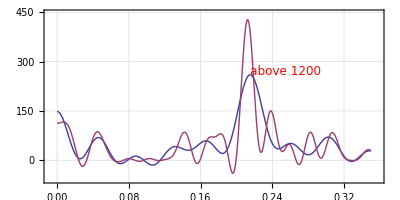

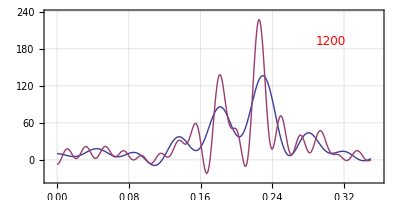

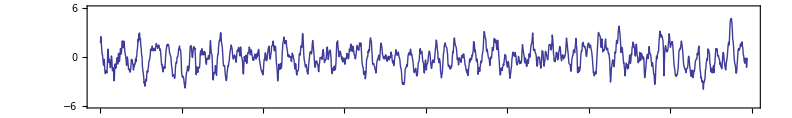

433.99

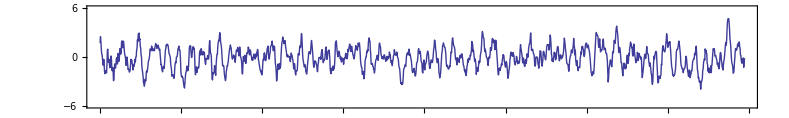

433.99

4.24578

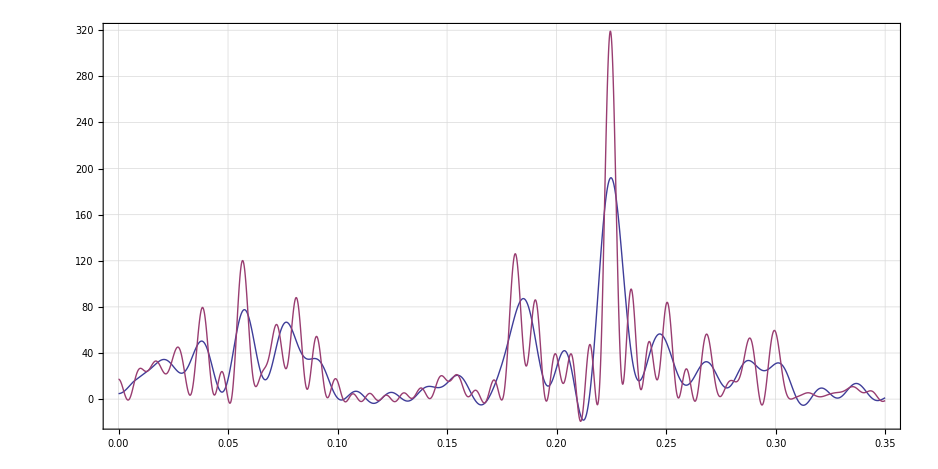

0.0714323

4.24578

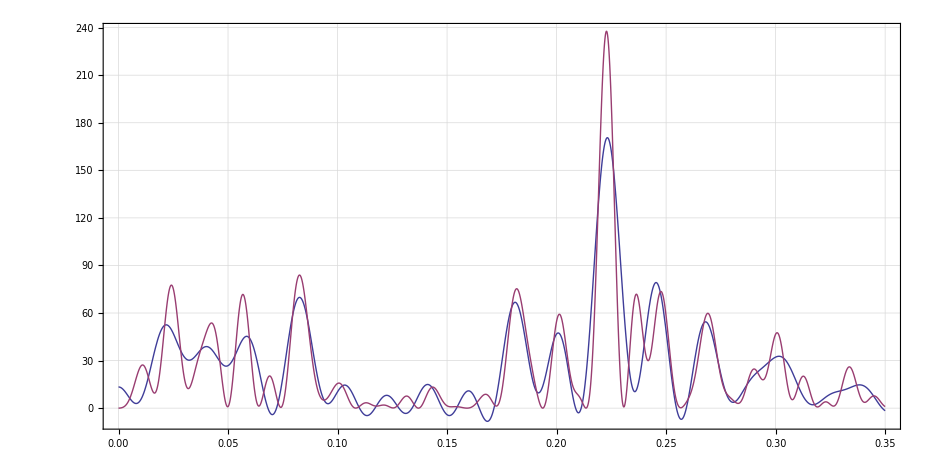

```mathematica
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
STRT=12; STRTY=1880+STRT/12;LNGTH=1200; ENDY=1880+LNGTH/12; 
 CF = 2.19; 2*Pi/Sqrt[CF]
lhs=Table[{1880.0+x,  (12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-CF*R[[x*12]])},{x,STRT/12,LNGTH/12+0, 1/12}];     
Plot[Evaluate@Table[PowerSpectralDensity[lhs,ω,i],{i,400,800,400}],{ω,0.0,0.35},Frame->True,PlotRange->All,AspectRatio->0.5, FrameTicks -> All, GridLines->Automatic] 
2*Pi/7.33/12

R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
STRT=550; STRTY=1880+STRT/12;LNGTH=1200; ENDY=1880+LNGTH/12; 
 CF = 2.19; 2*Pi/Sqrt[CF]
lhs=Table[{1880.0+x,  (12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-CF*R[[x*12]])},{x,STRT/12,LNGTH/12+0, 1/12}];     
Plot[Evaluate@Table[PowerSpectralDensity[lhs,ω,i],{i,325,650,325}],{ω,0.0,0.35},Frame->True,PlotRange->All,AspectRatio->0.5, FrameTicks -> All, GridLines->Automatic]
```

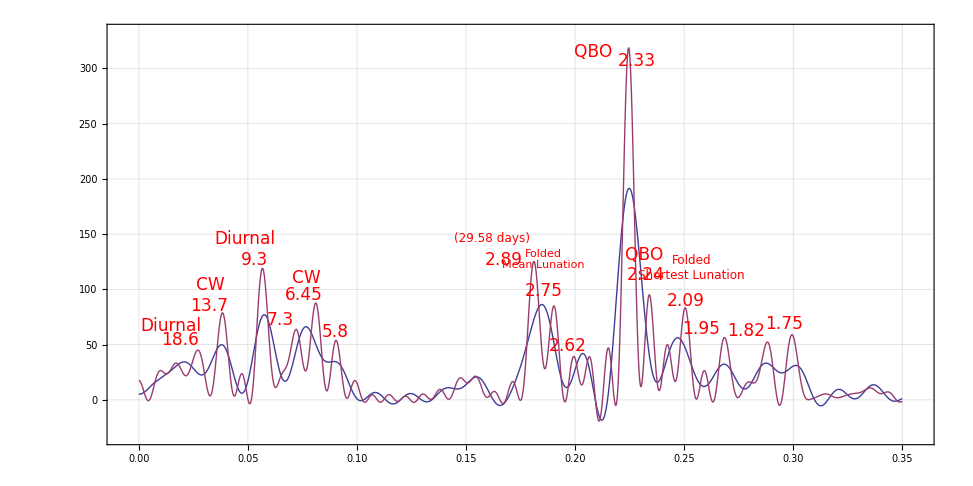

0.0714323

-69.5048

6.47885

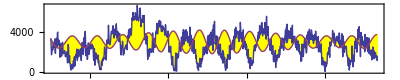

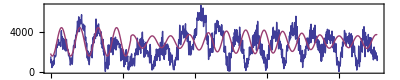

```mathematica
CW = 0.9698;
cw[x_] := Sin[CW*(x+2.)+ 0.111*Sin[0.38*(x+6.4)] +0.4] *(1+0.34*Sin[0.097*x-0.8]) ; 
cwbb[x_] := If[x>46.5, cw[x], 0.9*Sin[2*Pi/6.36*x-1.8]]; 

cw[x_] := Sin[CW*(x+2.)+ 0.111*Sin[0.38*(x+6.4)] +0.4] *(1+0.34*Sin[0.097*x-0.8]) ; 
cwb[x_] := 0.58*cw[x+0.3]+0.0*cw[x/2+1.0] + 0.0*Cos[2*Pi/5.79*x+1.4] ;  
cwbb[x_] := If[x>46.5, cwb[x], 0.9*Sin[2*Pi/6.36*x-1.8]]; 

cw[x_] := Sin[CW*(x+2.)+ 0.111*Sin[0.38*(x+6.4)] +0.4] *(1+0.34*Sin[0.097*x-0.8]) ; 
(* cwb[x_] := -0.58*cw[x+0.3]+0.0*cw[x/2+1.0] + 0.0*Cos[2*Pi/5.79*x+1.4] ;  *)
cwbb[x_] := If[x>46.5, -0.5*cw[x+0.45], 0.8*Sin[2*Pi/6.36*x-1.8]]; 


CWT = MeanFilter[CW1[[All,2]],3];
CWM = Table[{1880+i, 1770*cwbb[i-1.6]+3000},{i,50,133+2/12, 1/12}];
100*Correlation[CW1,CWM][[2,2]]
2*Pi/CW
ListLinePlot[{CW1,CWM}, AspectRatio->0.2, Filling->{1->{{2},Yellow}}, Frame->True, Axes->False, PlotLegends->{"CW", "Model"}]
CWT0 = MeanFilter[CW0[[All,2]],3];
CWL = Table[{1880+i, 1770*cwbb[i-1.3]+3000},{i,20,133+2/12, 1/12}];
ListLinePlot[{CW0,CWL}, AspectRatio->0.2, Frame->True, Axes->False, PlotLegends->{"CW", "Model"}]
```

{char t,4.96729,0.865561, Years from,1881.,to,1980.,CC,74.0927,74.5663,0.473643}

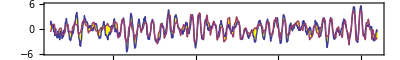

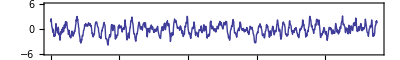

433.99

```mathematica
dilate[x_] := Sin[2*Pi*x+0.74];
Window = 7;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
STRT=12; STRTY=1880+STRT/12;LNGTH=1200; ENDY=1880+LNGTH/12; 
QBW=2.331;     TR = 199.0;  CF = 1.6;  OSC := 9.30;  CW =0.9698; 
diu[x_] := 0.33*Cos[2*Pi/OSC*x+5.5]+0.06*Cos[Pi/(2*OSC)*x+4.7]-0.2*Cos[2*Pi*x/(3*OSC)-0.2];
qbw[x_] := +0.045*Cos[2*Pi/7*x+1.9]+0.17*Cos[2*Pi/QBW*x+2.8] +0.08*Sin[2*Pi/2.246*x+0.1] -0.05*Cos[2*Pi/2.117*x-0.9] -0.03*Cos[2*Pi/3.58*x-1.6]-0.1*Cos[2*Pi/2.903*x-0.7]   ;
cw[x_] := Sin[CW*(x+2.)+ 0.111*Sin[0.38*(x+6.4)] +0.4] *(1+0.34*Sin[0.097*x-0.8]) ; 
(* cwb[x_] := -0.58*cw[x+0.3]+0.0*cw[x/2+1.0] + 0.0*Cos[2*Pi/5.79*x+1.4] ;  *)
cwbb[x_] := If[x>46.5, -0.5*cw[x+0.45], 0.8*Sin[2*Pi/6.36*x-1.8]]; 
(* RHS[x_] := 3.1*qbw[x-0.04]+1*0.4*cwb[x-0.24]-0.86*diu[x-1.2]+0.13*Cos[2*Pi/52*x+4.3] -0.15*Sin[2*Pi/21.0*x+4.2]+  0.2*Cos[2*Pi/7.333*x+3.0] ;  *)
RHS[x_] := (6.4*qbw[x*1.0022-0.2] +1*0.4*cwbb[x+0.1]-1.2*diu[x-0.7]+1.2*0.16*Cos[2*Pi*x*1.0011-2.4]-0*0.05*Cos[4*Pi*x-3.0] ) * (1+x*0.0038) ;  
lhs=Table[{1880.0+x,  (12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-CF*R[[x*12]]-0.0*(R[[x*12]])^3)},{x,STRT/12,LNGTH/12, 1/12}];     
rhs=Table[{1880.0+x, If[x>98.5&&x<116.2,-1.4,0]-If[x>98.5&&x<116.2,-1,1]*1.2*RHS[x-0.16*dilate[x]+0.83]}, 
                  {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-6,6},Frame->True,Axes->True, Filling->{1->{{2},Yellow}}, PlotLegends->{"LHS","RHS"},AspectRatio->0.15] 
SDIF = lhs[[All,2]]-rhs[[All,2]];  
ListLinePlot[{SDIF},PlotRange->{-6,6},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.15] 
CWY*365.25
```

{char t,6.19101,-0.0364165, Years from,1881.,to,1982.5,CC,85.355,85.355,0.}

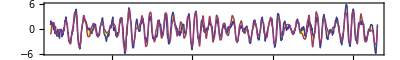

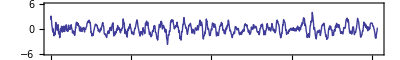

3.84999

42.8633

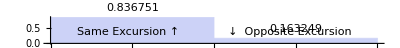

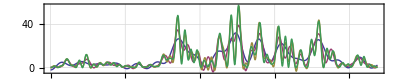

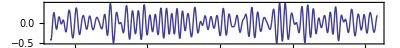

```mathematica
dilate[x_] := Sin[2*Pi*x+1.0];
Window = 7;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
STRT=12; STRTY=1880+STRT/12;LNGTH=1230; ENDY=1880+LNGTH/12; 
QBW=2.333;     TR = 99.0;  CF = 1.03;  OSC := 18.62;  CW =0.97; 
diu[x_] := 0.2*Cos[2*Pi/(OSC/2)*x+5.3]+0.11*Cos[2*Pi/OSC*x+0.5];
qbase[x_]:=0.19*Cos[2*Pi/QBW*x+2.9-0.24*Sin[2*Pi/OSC*x-0.4]];
SMALL=1;
qbw[x_] := qbase[x]*(1-0.26*Sin[2*Pi/10.58*x-1.43]) +
           0.1*Sin[2*Pi/2.246*x+0.02-0.1*Sin[2*Pi/OSC*x-0.4]] -
           SMALL*0.032*Cos[2*Pi/2.11*x-1.4] - 
           SMALL*0.05*Cos[2*Pi/3.575*x-1.77+0.5*Sin[2*Pi/OSC*x+1.3]]-  
           SMALL*0.04*Cos[2*Pi/1.94*x-2.0] + SMALL*0.01*Cos[2*Pi/7*x-3] -
           SMALL*0.06*Cos[2*Pi/4.04*x-1.89+0.52*Sin[2*Pi/OSC*x+2.3]] -
           SMALL*0.06*Cos[2*Pi/2.78*x-2.2+0.57*Sin[2*Pi/OSC*x+0.67]] -
           0.152*Cos[2*Pi/2.9*x-0.8+0.57*Sin[2*Pi/OSC*x+0.67] - 0.18*Sin[2*Pi/4.422*x+0.1]]   ;
cw[x_] := Sin[CW*(x+2.)+ 0.111*Sin[0.38*(x+6.4)] +0.4] *(1+0.34*Sin[0.097*x-0.8]) ; 
cwb[x_] := 0.27*cw[x+1.6]+0*.13*cw[x/2+1.5] + 0*.03*Cos[2*Pi/5.8*x+4.0] ;  
RHS[x_] := (8.3*qbw[x*1.0023-0.23] +0.29*cwb[x+0.75]-1.3*diu[x-0.7] ) + 0.11*Cos[2*Pi/52*x-1.9] - 0.2*Cos[2*Pi/7.33*x-0.7];  
RHS[x_] := (8.3*qbw[x*1.001-0.15]*(1-0.19*Sin[2*Pi/OSC*x+1.2]) +0.31*cwb[x+1.0]-1.3*diu[x-0.7] ) + 0.11*Cos[2*Pi/52*x-1.9] - 0.2*Cos[2*Pi/7.33*x-0.7];  
lhs=Table[{1880.0+x,  (12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-CF*R[[x*12]])},    {x,STRT/12,LNGTH/12, 1/12}]; 
LOW = 100.2; HI = 116.3;    
rhs=Table[{1880.0+x, If[x>LOW&&x<HI,-0.7,0]-If[x>LOW&&x<HI,-1,1]*1.17*RHS[x-0.1*dilate[x]+0.83]},   {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-6,6},Frame->True,Axes->True, Filling->{1->{{2},Yellow}}, PlotLegends->{"LHS","RHS"},AspectRatio->0.15] 
SDIF = lhs[[All,2]]-rhs[[All,2]];  
ListLinePlot[{SDIF},PlotRange->{-6,6},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.15] 
2*Pi/.136/12
100.0/2.333
SBIN = Abs[Sign[lhs[[All,2]]]- Sign[rhs[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,300,1200,300}],{ω,0.0,0.35},Frame->True,PlotRange->All,AspectRatio->0.2, FrameTicks -> All, GridLines->Automatic] 
ListLinePlot[{Table[{1880.0+x, qbw[x]},{x,1/12,135.0, 1/12}]}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"QBO"}]
(*Plot[Evaluate@Table[PowerSpectralDensity[lhs,ω,i],{i,600,1200,600}],{ω,0.0,0.35},Frame->True,PlotRange->All,AspectRatio->0.2, FrameTicks -> All, GridLines->Automatic]
```

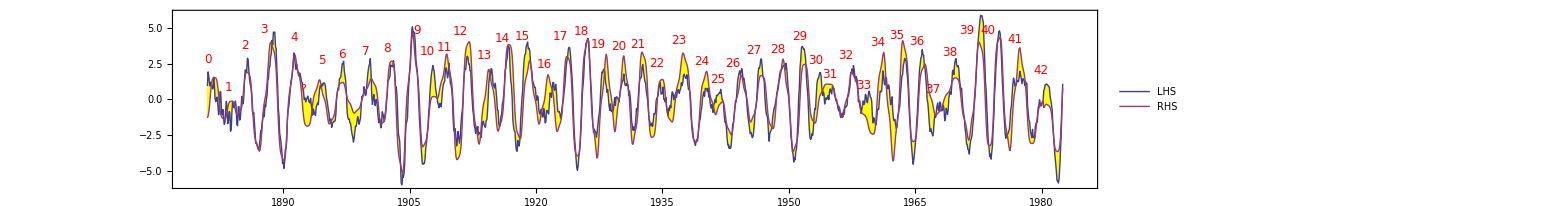

-Graphics-

3.84999

42.2297

-Graphics-

-Graphics-

-Graphics-

{5.89509 = char t,0.429296 =err,1881.  .. ,1982.5,CC,58.9013,51.5827,-7.31859}

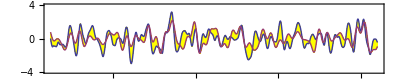

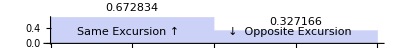

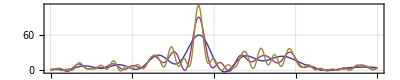

6.42452

5.5702

```mathematica
Window = 5;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
LNGTH=1200; STRT=12;
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
 IC=52.5;  SHFT=0.91; CF = 1.136;  FRQ := 2*Pi/Sqrt[CF];
(* RHS[x_] := (8.3*qbw[x*1.0023-0.23] +0.31*cwb[x+1.0]-1.3*diu[x-0.7] ) + 0.11*Cos[2*Pi/52*x-1.9] - 0.2*Cos[2*Pi/7.33*x-0.7];   *)
(* RHS[x_] := (8.3*qbw[x*1.0023-0.23] +0.29*cwb[x+0.75]-1.3*diu[x-0.7] ) + 0.11*Cos[2*Pi/52*x-1.9];  *)
SOLN=NDSolve[{y''[x]+CF*y[x]== -40.3*RHS[x+0.02], 
                               y'[IC]==-21.3, y[IC]==19.5}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x,  -0.8*Cos[2*Pi/FRQ*x-0.3]+0.031*(First[y[x+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,300,900,300}],{ω,0.0,0.2},Frame->True,PlotRange->All,AspectRatio->0.2, FrameTicks -> All, GridLines->Automatic] 
2*Pi/0.0815/12
2*Pi/0.094/12
```

67.4029

{0.,14126.3}

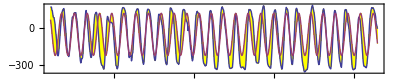

```mathematica
QBOM = Table[{1953.0+x, -900*qbase[73.0+x-0.45]-50},{x,1/12,61.25+1/12, 1/12}];  Q = MeanFilter[QBO[[All,2]],3];
QBOT = Table[{QBOM[[i,1]], Q[[i]]},{i,1,12*61.25+1, 1}];        
100*Correlation[QBOT,QBOM][[2,2]]
Variance[QBOT]-Variance[QBOM]
ListLinePlot[{QBOT, QBOM}, AspectRatio->0.2, Filling->{1->{{2},Yellow}}, Frame->True, Axes->False, PlotLegends->{"QBO", "Model"}]
```

{char t,6.19101,0.690311, Years from,1881.,to,1982.5,CC,77.4867,77.4867,5.68434×10^-14}

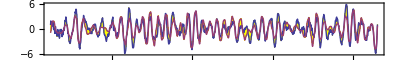

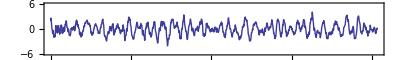

2.61799

2.32558

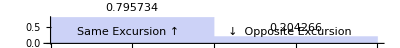

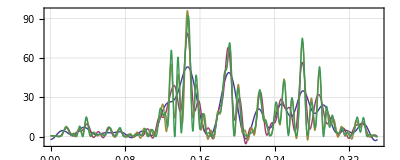

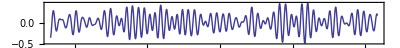

```mathematica
dilate[x_] := Sin[2*Pi*x+1.0];
Window = 7;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
STRT=12; STRTY=1880+STRT/12;LNGTH=1230; ENDY=1880+LNGTH/12; 
QBW=2.333;     TR = 99.0;  CF = 1.03;  OSC := 18.62;  CW =0.97; 
diu[x_] := 0.2*Cos[2*Pi/(OSC/2)*x+5.3]+0.11*Cos[2*Pi/OSC*x+0.5];
qbase[x_]:=0.19*Cos[2*Pi/QBW*x+2.9-0.24*Sin[2*Pi/OSC*x-0.4]];
qbw[x_] := qbase[x]*(1-0.26*Sin[2*Pi/10.58*x-1.43]) +
            0.1*Sin[2*Pi/2.246*x+0.01-0*.1*Sin[2*Pi/OSC*x-0.7]] -
           0.*032*Cos[2*Pi/2.11*x-1.4] -
            0.*05*Cos[2*Pi/3.575*x-1.77+0.5*Sin[2*Pi/OSC*x+1.3]]-  
              0.*04*Cos[2*Pi/1.94*x-2.0] + 
              0*.01*Cos[2*Pi/7*x-3] -
            0.*06*Cos[2*Pi/4.04*x-1.89+0.52*Sin[2*Pi/OSC*x+2.3]] -
          0.*06*Cos[2*Pi/2.78*x-2.2+0.57*Sin[2*Pi/OSC*x+0.67]] -
         0.152*Cos[2*Pi/2.9*x-0.8+0.57*Sin[2*Pi/OSC*x+0.67] -0.18*Sin[2*Pi/4.422*x+0.1]]   ;
cw[x_] := Sin[CW*(x+2.)+ 0.111*Sin[0.38*(x+6.4)] +0.4] *(1+0.34*Sin[0.097*x-0.8]) ; 
cwb[x_] := 0.27*cw[x+1.6]+0*.13*cw[x/2+1.5] + 0*.03*Cos[2*Pi/5.8*x+4.0] ;  
RHS[x_] := (8.3*qbw[x*1.0023-0.23] +0.29*cwb[x+0.75]-1.3*diu[x-0.7] ) + 0.11*Cos[2*Pi/52*x-1.9] - 0.2*Cos[2*Pi/7.33*x-0.7];  
RHS[x_] := (8.3*qbw[x*1.001-0.15]*(1-0.19*Sin[2*Pi/OSC*x+1.2]) +0.31*cwb[x+1.0]-1.3*diu[x-0.7] ) + 0.11*Cos[2*Pi/52*x-1.9] - 0.2*Cos[2*Pi/7.33*x-0.7];  
lhs=Table[{1880.0+x,  (12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-CF*R[[x*12]])},    {x,STRT/12,LNGTH/12, 1/12}]; 
LOW = 100.2; HI = 116.3;    
rhs=Table[{1880.0+x, If[x>LOW&&x<HI,-0.7,0]-If[x>LOW&&x<HI,-1,1]*1.17*RHS[x-0.1*dilate[x]+0.83]},   {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-6,6},Frame->True,Axes->True, Filling->{1->{{2},Yellow}}, PlotLegends->{"LHS","RHS"},AspectRatio->0.15] 
SDIF = lhs[[All,2]]-rhs[[All,2]];  
ListLinePlot[{SDIF},PlotRange->{-6,6},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.15] 
2*Pi/.2/12
100/43.0
SBIN = Abs[Sign[lhs[[All,2]]]- Sign[rhs[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,300,1200,300}],{ω,0.0,0.35},Frame->True,PlotRange->All,AspectRatio->0.4, FrameTicks -> All, GridLines->Automatic] 
ListLinePlot[{Table[{1880.0+x, qbw[x]},{x,1/12,135.0, 1/12}]}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"QBO"}]
```

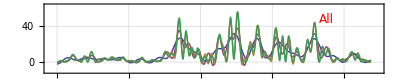

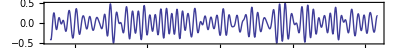

{char t,4.24578,1.27684, Years from,1881.,to,2013.33,CC,70.5627,74.1219,3.55924}

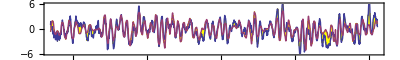

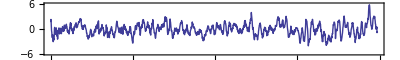

52.3599

2.32558

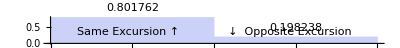

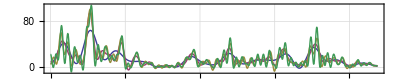

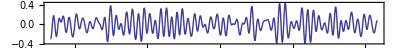

```mathematica
dilate[x_] := Sin[2*Pi*x+1.0];
Window = 7;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
STRT=12; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
QBW=2.333;     TR = 99.0;  CF = 2.19;  OSC := 18.62;  CW =0.97; 
diu[x_] := 0.2*Cos[2*Pi/(OSC/2)*x+5.3]+0.11*Cos[2*Pi/OSC*x+0.5];
qbase[x_]:=0.15*Cos[2*Pi/QBW*x+2.9-0.24*Sin[2*Pi/OSC*x-0.4]];
SMALL=0;
qbw[x_] := qbase[x]*(1-0.26*Sin[2*Pi/10.58*x-1.43]) +
           0.09*Sin[2*Pi/2.246*x+0.01-0*.1*Sin[2*Pi/OSC*x-0.7]] -
           0.03*Cos[2*Pi/2.11*x-1.4] - SMALL*0.05*Cos[2*Pi/3.575*x-1.77+0.5*Sin[2*Pi/OSC*x+1.3]]-  
           0.04*Cos[2*Pi/1.94*x-2.0] + 0.07*Cos[2*Pi/7*x-4.5] -
           SMALL*0.06*Cos[2*Pi/4.04*x-1.89+0.52*Sin[2*Pi/OSC*x+2.3]] -
           0.03*Cos[2*Pi/2.78*x-2.4+0.57*Sin[2*Pi/OSC*x+0.67]] -
           0.11*Cos[2*Pi/2.9*x-0.8+0.7*Sin[2*Pi/OSC*x+0.67] - 0.18*Sin[2*Pi/4.422*x+0.1]]   ;
cw[x_] := Sin[CW*(x+2.)+ 0.111*Sin[0.38*(x+6.4)] +0.4] *(1+0.34*Sin[0.097*x-0.8]) ; 
cwb[x_] := 1.8*cw[x+2.2]+0.6*cw[x/2+1.1] + 0*.03*Cos[2*Pi/5.8*x+4.0] ;  
RHS[x_] := (8.3*qbw[x*1.0023-0.23] +0.29*cwb[x+0.75]-1.3*diu[x-0.7] ) + 0.11*Cos[2*Pi/52*x-1.9] - 0.2*Cos[2*Pi/7.33*x-0.7];  
RHS[x_] := (8.3*qbw[x*1.001-0.15]*(1-0.19*Sin[2*Pi/OSC*x+1.2]) +0.31*cwb[x+1.0]-1.3*diu[x-0.7] ) + 0.11*Cos[2*Pi/52*x-1.9] - 0.2*Cos[2*Pi/7.33*x-0.7];  
lhs=Table[{1880.0+x,  (12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-CF*R[[x*12]])},    {x,STRT/12,LNGTH/12, 1/12}]; 
LOW = 100.2; HI = 116.3;    
rhs=Table[{1880.0+x, If[x>LOW&&x<HI,-0.7,0]-If[x>LOW&&x<HI,-1,1]*1.17*RHS[x-0.1*dilate[x]+0.83]},   {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-6,6},Frame->True,Axes->True, Filling->{1->{{2},Yellow}}, PlotLegends->{"LHS","RHS"},AspectRatio->0.15] 
SDIF = lhs[[All,2]]-rhs[[All,2]];  
ListLinePlot[{SDIF},PlotRange->{-6,6},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.15] 
2*Pi/.01/12
100/43.0
SBIN = Abs[Sign[lhs[[All,2]]]- Sign[rhs[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,300,1200,300}],{ω,0.0,0.35},Frame->True,PlotRange->All,AspectRatio->0.2, FrameTicks -> All, GridLines->Automatic] 
ListLinePlot[{Table[{1880.0+x, qbw[x]},{x,1/12,135.0, 1/12}]}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"QBO"}]
(*Plot[Evaluate@Table[PowerSpectralDensity[lhs,ω,i],{i,600,1200,600}],{ω,0.0,0.35},Frame->True,PlotRange->All,AspectRatio->0.2, FrameTicks -> All, GridLines->Automatic]
```

{4.46527 = char t,-0.0140828 =err,1881.  .. ,2013.33,CC,70.6931,70.6931,0.}

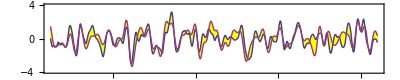

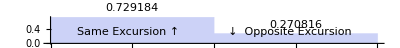

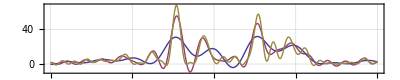

6.7128

5.5702

```mathematica
Window = 5;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
LNGTH=1200; STRT=12;
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
 IC=52.5;  SHFT=0.91; CF = 1.98;  FRQ := 2*Pi/Sqrt[CF];
RHS[x_] := 5.9*qbw[x-0.13]*(1-0.19*Sin[2*Pi/OSC*x+1.2]) +0.21*cwb[x+1.08]-1.3*diu[x-0.7]+0.21Cos[2*Pi/52*x-1.9] - 0.2*Cos[2*Pi/7.33*x-0.7] +0.2*Cos[2*Pi/27*x-1.0];  
SOLN=NDSolve[{y''[x]+CF*y[x]== -40.3*RHS[x-0.12],  y'[IC]==-25.3, y[IC]==15.5}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, 0*.1*Sin[2*Pi/FRQ*x+3.2] +0.05*(First[y[x+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,300,900,300}],{ω,0.0,0.2},Frame->True,PlotRange->All,AspectRatio->0.2, FrameTicks -> All, GridLines->Automatic] 
2*Pi/0.078/12
2*Pi/0.094/12
```

{char t,4.5583,0.117889, Years from,1881.,to,1981.67,CC,85.6373,85.6375,0.000132272}

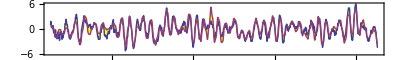

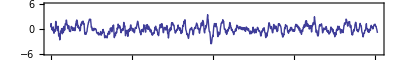

2.16363

2.32558

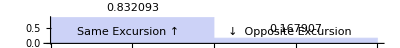

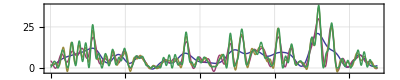

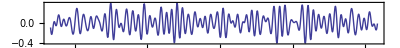

```mathematica
dilate[x_] := Sin[2*Pi*x+1.0];
Window = 7;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
STRT=12; STRTY=1880+STRT/12;LNGTH=1220; ENDY=1880+LNGTH/12; 
QBW=2.368;     TR = 99.0;  CF = 1.9;  OSC := 18.62;  CW =0.974; 
diu[x_] := 0.2*Cos[2*Pi/(OSC/2)*x+5.3]+0.11*Cos[2*Pi/OSC*x+0.5];
qbase[x_]:=0.03*Cos[2*Pi/QBW*x+5.9 -0.61*Sin[2*Pi/(OSC)*x+4.3]] - 0.14*Cos[2*Pi/2.327*x+5.6] - 0*.02*Cos[2*Pi/2.349*x+2.7 ];
SMALL=1;
qbw[x_] := qbase[x]*(1-0.27*Sin[2*Pi/10.58*x-1.2]) +
           0.08*Sin[2*Pi/2.247*x+0.01-0*.1*Sin[2*Pi/OSC*x-0.7]] -
           0.022*Cos[2*Pi/2.11*x-0.9] - SMALL*0.05*Cos[2*Pi/3.575*x-2.+0.0*Sin[2*Pi/OSC*x+1.3]]-  
           0.05*Cos[2*Pi/1.941*x-2] + 0.04*Cos[2*Pi/7*x-4.5] -
           SMALL*0.03*Cos[2*Pi/4.04*x-2.+0.52*Sin[2*Pi/OSC*x+2.3]]-
           0.04*Cos[2*Pi/2.77*x-2.9-0.3*Sin[2*Pi/8.99*x+3.91]] -
           0.06*Cos[2*Pi/2.7133*x-4.5-1.1*Sin[2*Pi/8.99*x+3.91]] -
           0.09*Cos[2*Pi/2.9*x-1.1+0.6*Sin[2*Pi/OSC*x+0.4] - 0.0*Sin[2*Pi/4.422*x+0.1]]   ;
cw[x_] := Sin[CW*(x+1.75)+ 0.111*Sin[0.38*(x+6.4)] +0.4] *(1+0.34*Sin[0.097*x-0.8]) ; 
cwb[x_] := 1.1*cw[x+2.2]+0.45*cw[x/2+1] + 0*.01*Cos[2*Pi/5.8*x+5.0] ;  
RHS[x_] := 6*qbw[x-0.08]*(1-0.19*Sin[2*Pi/OSC*x+1.2]) +0.33*cwb[x+0.9]-1.5*diu[x-0.6] + 0.12*Cos[2*Pi/52*x-1.9] + 0.2*Cos[2*Pi/27.2*x-0.9] - 0.3*Cos[2*Pi/7.33*x-0.7];  
lhs=Table[{1880.0+x,  (12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-CF*R[[x*12]])},    {x,STRT/12,LNGTH/12, 1/12}]; 
LOW = 100.2; HI = 116.3;    
rhs=Table[{1880.0+x, If[x>LOW&&x<HI,-0.7,0]-If[x>LOW&&x<HI,-1,1]*1.7*RHS[x-0.11*dilate[x]+0.83]},   {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-6,6},Frame->True,Axes->True, Filling->{1->{{2},Yellow}}, PlotLegends->{"LHS","RHS"},AspectRatio->0.15] 
SDIF = lhs[[All,2]]-rhs[[All,2]];  
ListLinePlot[{SDIF},PlotRange->{-6,6},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.15] 
2*Pi/.242/12
100/43.0
SBIN = Abs[Sign[lhs[[All,2]]]- Sign[rhs[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,300,1200,300}],{ω,0.0,0.35},Frame->True,PlotRange->All,AspectRatio->0.2, FrameTicks -> All, GridLines->Automatic] 
ListLinePlot[{Table[{1880.0+x, qbw[x]},{x,1/12,135.0, 1/12}]}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"QBO"}]
```

{char t,4.5583,-0.0820362, Years from,1881.,to,1981.67,CC,78.3392,78.3361,-0.00312412}

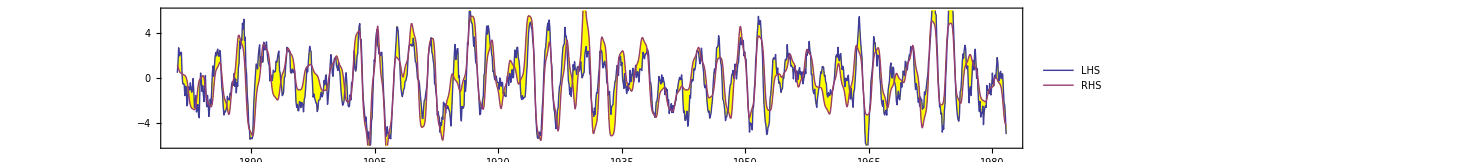

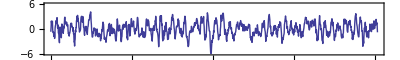

1.81176

2.32558

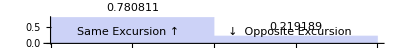

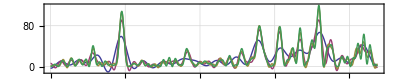

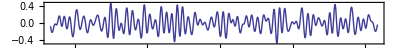

```mathematica
dilate[x_] := Sin[2*Pi*x+1.0];
Window = 6;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
STRT=12; STRTY=1880+STRT/12;LNGTH=1220; ENDY=1880+LNGTH/12; 
QBW=2.368;     TR = 99.0;  CF = 1.9;  OSC := 18.62;  CW =0.974; 
diu[x_] := 0.2*Cos[2*Pi/(OSC/2)*x+5.3]+0.11*Cos[2*Pi/OSC*x+0.5];
qbase[x_]:=0.03*Cos[2*Pi/QBW*x+4.9 -0.6*Sin[2*Pi/(OSC)*x+4.3]] - 0.12*Cos[2*Pi/2.325*x+5.5 ] - 0*.02*Cos[2*Pi/2.349*x+2.7 ];
SMALL=1;
qbw[x_] := 1.2*qbase[x]*(1-0.27*Sin[2*Pi/10.58*x-1.2]) +
           0.08*Sin[2*Pi/2.247*x+0.01-0*.1*Sin[2*Pi/OSC*x-0.7]] -
           0.04*Cos[2*Pi/2.11*x-1.4] - SMALL*0.05*Cos[2*Pi/3.575*x-2.+0.0*Sin[2*Pi/OSC*x+1.3]] + 
           0.02*Cos[2*Pi/1.74*x-2] + 0.04*Cos[2*Pi/7*x-4.5] -
           0.04*Cos[2*Pi/1.93*x-3] + 0.04*Cos[2*Pi/7*x-4.5] -
           SMALL*0.03*Cos[2*Pi/4.04*x-2.+0.52*Sin[2*Pi/OSC*x+2.3]]-
           0.04*Cos[2*Pi/2.77*x-2.9-0.3*Sin[2*Pi/8.99*x+3.91]] -
           0.06*Cos[2*Pi/2.7133*x-4.5-1.1*Sin[2*Pi/8.99*x+3.91]] -
           0.09*Cos[2*Pi/2.9*x-1.1+0.6*Sin[2*Pi/OSC*x+0.4] - 0.0*Sin[2*Pi/4.422*x+0.1]]   ;
cw[x_] := Sin[CW*(x+1.75)+ 0.111*Sin[0.38*(x+6.4)] +0.4] *(1+0.34*Sin[0.097*x-0.8]) ; 
cwb[x_] := 1.3*cw[x+2.3]+0.45*cw[x/2+1] + 0*.01*Cos[2*Pi/5.8*x+5.0] ;  
RHS[x_] := 7.8*qbw[x-0.07]*(1-0.19*Sin[2*Pi/OSC*x+1.2]) +0.33*cwb[x+0.9]-1.5*diu[x-0.6] + 0.12*Cos[2*Pi/52*x-1.9] + 0.2*Cos[2*Pi/27.2*x-0.9] - 0.3*Cos[2*Pi/7.33*x-0.7];  
lhs=Table[{1880.0+x,  (12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-CF*R[[x*12]])},    {x,STRT/12,LNGTH/12, 1/12}]; 
LOW = 100.2; HI = 116.3;    
rhs=Table[{1880.0+x, If[x>LOW&&x<HI,-0.7,0]-If[x>LOW&&x<HI,-1,1]*1.75*RHS[x-0.11*dilate[x]+0.83]},   {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-6,6},Frame->True,Axes->True, Filling->{1->{{2},Yellow}}, PlotLegends->{"LHS","RHS"},AspectRatio->0.15] 
SDIF = lhs[[All,2]]-rhs[[All,2]];  
ListLinePlot[{SDIF},PlotRange->{-6,6},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.15] 
2*Pi/.289/12
100/43.0
SBIN = Abs[Sign[lhs[[All,2]]]- Sign[rhs[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,300,1200,300}],{ω,0.0,0.35},Frame->True,PlotRange->All,AspectRatio->0.2, FrameTicks -> All, GridLines->Automatic] 
ListLinePlot[{Table[{1880.0+x, qbw[x]},{x,1/12,135.0, 1/12}]}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"QBO"}]
```